```mathematica
xp1[x1_,x2_,x3_,y1_,y2_,y3_]:=(x1^(1-λ)Exp[β(-y2+y3)])/(x1^(1-λ)Exp[β(-y2+y3)]+x2^(1-λ)Exp[β(y1-y3)]+x3^(1-λ)Exp[β(-y1+y2)])
xp2[x1_,x2_,x3_,y1_,y2_,y3_]:=(x2^(1-λ)Exp[β(y1-y3)])/(x1^(1-λ)Exp[β(-y2+y3)]+x2^(1-λ)Exp[β(y1-y3)]+x3^(1-λ)Exp[β(-y1+y2)])
```

```mathematica
xp3[x1_,x2_,x3_,y1_,y2_,y3_]:=(x3^(1-λ)Exp[β(-y1+y2)])/(x1^(1-λ)Exp[β(-y2+y3)]+x2^(1-λ)Exp[β(y1-y3)]+x3^(1-λ)Exp[β(-y1+y2)])
```

```mathematica
yp1[x1_,x2_,x3_,y1_,y2_,y3_]:=(y1^(1-λ)Exp[β(-x2+x3)])/(y1^(1-λ)Exp[β(-x2+x3)]+y2^(1-λ)Exp[β(x1-x3)]+y3^(1-λ)Exp[β(-x1+x2)])
yp2[x1_,x2_,x3_,y1_,y2_,y3_]:=(y2^(1-λ)Exp[β(x1-x3)])/(y1^(1-λ)Exp[β(-x2+x3)]+y2^(1-λ)Exp[β(x1-x3)]+y3^(1-λ)Exp[β(-x1+x2)])

yp3[x1_,x2_,x3_,y1_,y2_,y3_]:=(y3^(1-λ)Exp[β(-x1+x2)])/(y1^(1-λ)Exp[β(-x2+x3)]+y2^(1-λ)Exp[β(x1-x3)]+y3^(1-λ)Exp[β(-x1+x2)])
```

```mathematica
Simplify[D[(x3^(1-λ)Exp[β(-yp1[x1,x2,x3,y1,y2,y3]+yp2[x1,x2,x3,y1,y2,y3])])/(x1^(1-λ)Exp[β(-yp2[x1,x2,x3,y1,y2,y3]+yp3[x1,x2,x3,y1,y2,y3])]+x2^(1-λ)Exp[β(yp1[x1,x2,x3,y1,y2,y3]-yp3[x1,x2,x3,y1,y2,y3])]+x3^(1-λ)Exp[β(-yp1[x1,x2,x3,y1,y2,y3]+yp2[x1,x2,x3,y1,y2,y3])]),y3]]
```

(3 ⅇ^(-((ⅇ^((-x1+x2) β) (1+x1-x3) y1^λ y2^λ y3+ⅇ^((x1-x3) β) (-1+x1-x3) y1^λ y2 y3^λ-ⅇ^((-x2+x3) β) (-x1+x3) y1 y2^λ y3^λ) β)/(ⅇ^((-x1+x2) β) y1^λ y2^λ y3+ⅇ^((x1-x3) β) y1^λ y2 y3^λ+ⅇ^((-x2+x3) β) y1 y2^λ y3^λ)) x1^λ x2^λ x3^(1+λ) y1^λ y2^λ (ⅇ^(((ⅇ^((-x1+x2) β) (2+x1+x2-2 x3) y1^λ y2^λ y3+ⅇ^((x1-x3) β) (-1+x1+x2-2 x3) y1^λ y2 y3^λ+ⅇ^((-x2+x3) β) (-1+x1+x2-2 x3) y1 y2^λ y3^λ) β)/(ⅇ^((-x1+x2) β) y1^λ y2^λ y3+ⅇ^((x1-x3) β) y1^λ y2 y3^λ+ⅇ^((-x2+x3) β) y1 y2^λ y3^λ)) x1 x2^λ y1^λ y2-x1^λ x2 y1 y2^λ) y3^λ β (-1+λ))/((ⅇ^((ⅇ^(x1 β) (ⅇ^((x1+x2) β) y1^λ y2-ⅇ^(2 x3 β) y1 y2^λ) y3^λ β)/(ⅇ^((2 x2+x3) β) y1^λ y2^λ y3+ⅇ^((2 x1+x2) β) y1^λ y2 y3^λ+ⅇ^((x1+2 x3) β) y1 y2^λ y3^λ)) x1^λ x2^λ x3+ⅇ^((y2^λ (-ⅇ^((-x1+x2) β) y1^λ y3+ⅇ^((-x2+x3) β) y1 y3^λ) β)/(ⅇ^((-x1+x2) β) y1^λ y2^λ y3+ⅇ^((x1-x3) β) y1^λ y2 y3^λ+ⅇ^((-x2+x3) β) y1 y2^λ y3^λ)) x1^λ x2 x3^λ+ⅇ^((ⅇ^(x2 β) y1^λ (ⅇ^((x2+x3) β) y2^λ y3-ⅇ^(2 x1 β) y2 y3^λ) β)/(ⅇ^((2 x2+x3) β) y1^λ y2^λ y3+ⅇ^((2 x1+x2) β) y1^λ y2 y3^λ+ⅇ^((x1+2 x3) β) y1 y2^λ y3^λ)) x1 x2^λ x3^λ)^2 (ⅇ^((-x1+x2) β) y1^λ y2^λ y3+ⅇ^((x1-x3) β) y1^λ y2 y3^λ+ⅇ^((-x2+x3) β) y1 y2^λ y3^λ)^2)

-(ⅇ^((-(ⅇ^((x1-x3) β) y2^(1-λ))/(ⅇ^((-x2+x3) β) y1^(1-λ)+ⅇ^((x1-x3) β) y2^(1-λ)+ⅇ^((-x1+x2) β) y3^(1-λ))+(ⅇ^((-x1+x2) β) y3^(1-λ))/(ⅇ^((-x2+x3) β) y1^(1-λ)+ⅇ^((x1-x3) β) y2^(1-λ)+ⅇ^((-x1+x2) β) y3^(1-λ))) β) x1^(1-λ) (ⅇ^((-(ⅇ^((x1-x3) β) y2^(1-λ))/(ⅇ^((-x2+x3) β) y1^(1-λ)+ⅇ^((x1-x3) β) y2^(1-λ)+ⅇ^((-x1+x2) β) y3^(1-λ))+(ⅇ^((-x1+x2) β) y3^(1-λ))/(ⅇ^((-x2+x3) β) y1^(1-λ)+ⅇ^((x1-x3) β) y2^(1-λ)+ⅇ^((-x1+x2) β) y3^(1-λ))) β) x1^(1-λ) β ((ⅇ^((x1-x3) β+(-x2+x3) β) y1^-λ y2^(1-λ) (1-λ))/((ⅇ^((-x2+x3) β) y1^(1-λ)+ⅇ^((x1-x3) β) y2^(1-λ)+ⅇ^((-x1+x2) β) y3^(1-λ))^2)-(ⅇ^((-x1+x2) β+(-x2+x3) β) y1^-λ y3^(1-λ) (1-λ))/((ⅇ^((-x2+x3) β) y1^(1-λ)+ⅇ^((x1-x3) β) y2^(1-λ)+ⅇ^((-x1+x2) β) y3^(1-λ))^2))+ⅇ^((-(ⅇ^((-x2+x3) β) y1^(1-λ))/(ⅇ^((-x2+x3) β) y1^(1-λ)+ⅇ^((x1-x3) β) y2^(1-λ)+ⅇ^((-x1+x2) β) y3^(1-λ))+(ⅇ^((x1-x3) β) y2^(1-λ))/(ⅇ^((-x2+x3) β) y1^(1-λ)+ⅇ^((x1-x3) β) y2^(1-λ)+ⅇ^((-x1+x2) β) y3^(1-λ))) β) x3^(1-λ) β ((ⅇ^(2 (-x2+x3) β) y1^(1-2 λ) (1-λ))/((ⅇ^((-x2+x3) β) y1^(1-λ)+ⅇ^((x1-x3) β) y2^(1-λ)+ⅇ^((-x1+x2) β) y3^(1-λ))^2)-(ⅇ^((x1-x3) β+(-x2+x3) β) y1^-λ y2^(1-λ) (1-λ))/((ⅇ^((-x2+x3) β) y1^(1-λ)+ⅇ^((x1-x3) β) y2^(1-λ)+ⅇ^((-x1+x2) β) y3^(1-λ))^2)-(ⅇ^((-x2+x3) β) y1^-λ (1-λ))/(ⅇ^((-x2+x3) β) y1^(1-λ)+ⅇ^((x1-x3) β) y2^(1-λ)+ⅇ^((-x1+x2) β) y3^(1-λ)))+ⅇ^(((ⅇ^((-x2+x3) β) y1^(1-λ))/(ⅇ^((-x2+x3) β) y1^(1-λ)+ⅇ^((x1-x3) β) y2^(1-λ)+ⅇ^((-x1+x2) β) y3^(1-λ))-(ⅇ^((-x1+x2) β) y3^(1-λ))/(ⅇ^((-x2+x3) β) y1^(1-λ)+ⅇ^((x1-x3) β) y2^(1-λ)+ⅇ^((-x1+x2) β) y3^(1-λ))) β) x2^(1-λ) β (-(ⅇ^(2 (-x2+x3) β) y1^(1-2 λ) (1-λ))/((ⅇ^((-x2+x3) β) y1^(1-λ)+ⅇ^((x1-x3) β) y2^(1-λ)+ⅇ^((-x1+x2) β) y3^(1-λ))^2)+(ⅇ^((-x1+x2) β+(-x2+x3) β) y1^-λ y3^(1-λ) (1-λ))/((ⅇ^((-x2+x3) β) y1^(1-λ)+ⅇ^((x1-x3) β) y2^(1-λ)+ⅇ^((-x1+x2) β) y3^(1-λ))^2)+(ⅇ^((-x2+x3) β) y1^-λ (1-λ))/(ⅇ^((-x2+x3) β) y1^(1-λ)+ⅇ^((x1-x3) β) y2^(1-λ)+ⅇ^((-x1+x2) β) y3^(1-λ)))))/(ⅇ^((-(ⅇ^((x1-x3) β) y2^(1-λ))/(ⅇ^((-x2+x3) β) y1^(1-λ)+ⅇ^((x1-x3) β) y2^(1-λ)+ⅇ^((-x1+x2) β) y3^(1-λ))+(ⅇ^((-x1+x2) β) y3^(1-λ))/(ⅇ^((-x2+x3) β) y1^(1-λ)+ⅇ^((x1-x3) β) y2^(1-λ)+ⅇ^((-x1+x2) β) y3^(1-λ))) β) x1^(1-λ)+ⅇ^(((ⅇ^((-x2+x3) β) y1^(1-λ))/(ⅇ^((-x2+x3) β) y1^(1-λ)+ⅇ^((x1-x3) β) y2^(1-λ)+ⅇ^((-x1+x2) β) y3^(1-λ))-(ⅇ^((-x1+x2) β) y3^(1-λ))/(ⅇ^((-x2+x3) β) y1^(1-λ)+ⅇ^((x1-x3) β) y2^(1-λ)+ⅇ^((-x1+x2) β) y3^(1-λ))) β) x2^(1-λ)+ⅇ^((-(ⅇ^((-x2+x3) β) y1^(1-λ))/(ⅇ^((-x2+x3) β) y1^(1-λ)+ⅇ^((x1-x3) β) y2^(1-λ)+ⅇ^((-x1+x2) β) y3^(1-λ))+(ⅇ^((x1-x3) β) y2^(1-λ))/(ⅇ^((-x2+x3) β) y1^(1-λ)+ⅇ^((x1-x3) β) y2^(1-λ)+ⅇ^((-x1+x2) β) y3^(1-λ))) β) x3^(1-λ))^2+(ⅇ^((-(ⅇ^((x1-x3) β) y2^(1-λ))/(ⅇ^((-x2+x3) β) y1^(1-λ)+ⅇ^((x1-x3) β) y2^(1-λ)+ⅇ^((-x1+x2) β) y3^(1-λ))+(ⅇ^((-x1+x2) β) y3^(1-λ))/(ⅇ^((-x2+x3) β) y1^(1-λ)+ⅇ^((x1-x3) β) y2^(1-λ)+ⅇ^((-x1+x2) β) y3^(1-λ))) β) x1^(1-λ) β ((ⅇ^((x1-x3) β+(-x2+x3) β) y1^-λ y2^(1-λ) (1-λ))/((ⅇ^((-x2+x3) β) y1^(1-λ)+ⅇ^((x1-x3) β) y2^(1-λ)+ⅇ^((-x1+x2) β) y3^(1-λ))^2)-(ⅇ^((-x1+x2) β+(-x2+x3) β) y1^-λ y3^(1-λ) (1-λ))/((ⅇ^((-x2+x3) β) y1^(1-λ)+ⅇ^((x1-x3) β) y2^(1-λ)+ⅇ^((-x1+x2) β) y3^(1-λ))^2)))/(ⅇ^((-(ⅇ^((x1-x3) β) y2^(1-λ))/(ⅇ^((-x2+x3) β) y1^(1-λ)+ⅇ^((x1-x3) β) y2^(1-λ)+ⅇ^((-x1+x2) β) y3^(1-λ))+(ⅇ^((-x1+x2) β) y3^(1-λ))/(ⅇ^((-x2+x3) β) y1^(1-λ)+ⅇ^((x1-x3) β) y2^(1-λ)+ⅇ^((-x1+x2) β) y3^(1-λ))) β) x1^(1-λ)+ⅇ^(((ⅇ^((-x2+x3) β) y1^(1-λ))/(ⅇ^((-x2+x3) β) y1^(1-λ)+ⅇ^((x1-x3) β) y2^(1-λ)+ⅇ^((-x1+x2) β) y3^(1-λ))-(ⅇ^((-x1+x2) β) y3^(1-λ))/(ⅇ^((-x2+x3) β) y1^(1-λ)+ⅇ^((x1-x3) β) y2^(1-λ)+ⅇ^((-x1+x2) β) y3^(1-λ))) β) x2^(1-λ)+ⅇ^((-(ⅇ^((-x2+x3) β) y1^(1-λ))/(ⅇ^((-x2+x3) β) y1^(1-λ)+ⅇ^((x1-x3) β) y2^(1-λ)+ⅇ^((-x1+x2) β) y3^(1-λ))+(ⅇ^((x1-x3) β) y2^(1-λ))/(ⅇ^((-x2+x3) β) y1^(1-λ)+ⅇ^((x1-x3) β) y2^(1-λ)+ⅇ^((-x1+x2) β) y3^(1-λ))) β) x3^(1-λ))

```mathematica
Simplify[%/.{x1->1/3,x2->1/3,x3->1/3,y1->1/3,y2->1/3,y3->1/3}]
```

0

```mathematica
Eigenvalues[({{1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 1}})(1-λ)-1/3(1-λ)({{1, 1, 1, 0, 0, 0}, {1, 1, 1, 0, 0, 0}, {1, 1, 1, 0, 0, 0}, {0, 0, 0, 1, 1, 1}, {0, 0, 0, 1, 1, 1}, {0, 0, 0, 1, 1, 1}})+({{-2, 1, 1, 0, 0, 0}, {1, -2, 1, 0, 0, 0}, {1, 1, -2, 0, 0, 0}, {0, 0, 0, -2, 1, 1}, {0, 0, 0, 1, -2, 1}, {0, 0, 0, 1, 1, -2}})β^2/9+1/3(1-λ)β({{0, 0, 0, 0, -1, 1}, {0, 0, 0, 1, 0, -1}, {0, 0, 0, -1, 1, 0}, {0, -1, 1, 0, 0, 0}, {1, 0, -1, 0, 0, 0}, {-1, 1, 0, 0, 0, 0}})]
```

{0,0,1/3 (3-β^2-3 λ-√3 √(-β^2+2 β^2 λ-β^2 λ^2)),1/3 (3-β^2-3 λ-√3 √(-β^2+2 β^2 λ-β^2 λ^2)),1/3 (3-β^2-3 λ+√3 √(-β^2+2 β^2 λ-β^2 λ^2)),1/3 (3-β^2-3 λ+√3 √(-β^2+2 β^2 λ-β^2 λ^2))}

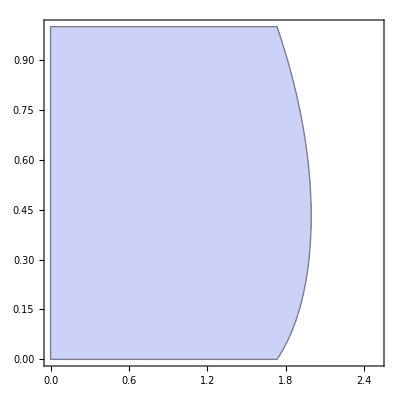

```mathematica
RegionPlot[Abs[1/3 (3-β^2-3 λ+√3 √(-β^2+2 β^2 λ-β^2 λ^2))]<1,{β,0,2.5},{λ,0,1}]
```

```mathematica
Eigenvalues[({{1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 1}})(1-λ)-1/3(1-λ)({{1, 1, 1, 0, 0, 0}, {1, 1, 1, 0, 0, 0}, {1, 1, 1, 0, 0, 0}, {0, 0, 0, 1, 1, 1}, {0, 0, 0, 1, 1, 1}, {0, 0, 0, 1, 1, 1}})+({{-2, 1, 1, 0, 0, 0}, {1, -2, 1, 0, 0, 0}, {1, 1, -2, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}})β^2/9+1/3(1-λ)β({{0, 0, 0, 0, -1, 1}, {0, 0, 0, 1, 0, -1}, {0, 0, 0, -1, 1, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}})+1/3 β({{0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, -1, 1, 0, 0, 0}, {1, 0, -1, 0, 0, 0}, {-1, 1, 0, 0, 0, 0}})]
```

{0,0,1/6 (6-β^2-6 λ-β √(-12+β^2+12 λ)),1/6 (6-β^2-6 λ-β √(-12+β^2+12 λ)),1/6 (6-β^2-6 λ+β √(-12+β^2+12 λ)),1/6 (6-β^2-6 λ+β √(-12+β^2+12 λ))}

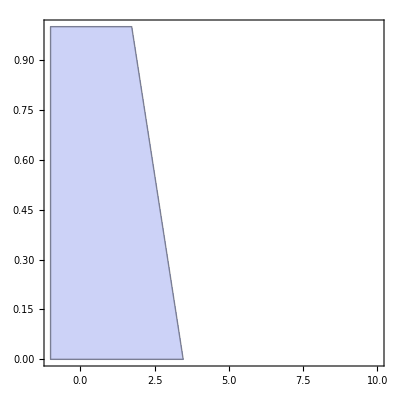

```mathematica
RegionPlot[Abs[1/6 (6-β^2-6 λ-β √(-12+β^2+12 λ))]<1,{β,-1,10},{λ,0,1}]
```

```mathematica
Simplify[D[(x3^(1-λ)Exp[β(-yp1[x1,x2,x3,y1,y2,y3]+yp2[x1,x2,x3,y1,y2,y3])])/(x1^(1-λ)Exp[β(-yp2[x1,x2,x3,y1,y2,y3]+yp3[x1,x2,x3,y1,y2,y3])]+x2^(1-λ)Exp[β(yp1[x1,x2,x3,y1,y2,y3]-yp3[x1,x2,x3,y1,y2,y3])]+x3^(1-λ)Exp[β(-yp1[x1,x2,x3,y1,y2,y3]+yp2[x1,x2,x3,y1,y2,y3])]),y3]]
```